# MNIST Visualization and Processing

### Imports

#### MNIST

```mathematica
resource = ResourceObject["MNIST"];
trainingData = ResourceData[resource, "TrainingData"];
testData = ResourceData[resource, "TestData"];
```

### Sets and subsets

#### MNIST

```mathematica
orderedImages = trainingData[[All, 1]];
orderedLabels = trainingData[[All, 2]];
```

```mathematica
orderedImagesTest = testData[[All, 1]];
orderedLabelsTest = testData[[All, 2]];
```

```mathematica
dataList = Transpose[{orderedImages, orderedLabels}];
shuffledData = RandomSample[dataList];
```

```mathematica
dataListTest = Transpose[{orderedImagesTest, orderedLabelsTest}];
```

```mathematica
images = shuffledData[[All, 1]];
labels = shuffledData[[All, 2]];
```

```mathematica
(* Splits training data into digits. *)

set0 = Cases[dataList,{_ , 0}];
set1 = Cases[dataList,{_ , 1}];
set2 = Cases[dataList,{_ , 2}];
set3 = Cases[dataList,{_ , 3}];
set4 = Cases[dataList,{_ , 4}];
set5 = Cases[dataList,{_ , 5}];
set6 = Cases[dataList,{_ , 6}];
set7 = Cases[dataList,{_ , 7}];
set8 = Cases[dataList,{_ , 8}];
set9 = Cases[dataList,{_ , 9}];

setList = Table[ Cases[dataList, {_, n}], {n, 0, 9} ];
```

```mathematica
(* Splits test data into digits. *)

set0Test = Cases[dataListTest,{_ , 0}];
set1Test = Cases[dataListTest,{_ , 1}];
set2Test = Cases[dataListTest,{_ , 2}];
set3Test = Cases[dataListTest,{_ , 3}];
set4Test = Cases[dataListTest,{_ , 4}];
set5Test = Cases[dataListTest,{_ , 5}];
set6Test = Cases[dataListTest,{_ , 6}];
set7Test = Cases[dataListTest,{_ , 7}];
set8Test = Cases[dataListTest,{_ , 8}];
set9Test = Cases[dataListTest,{_ , 9}];

setListTest = Table[ Cases[dataListTest, {_, n}], {n, 0, 9} ];
```

```mathematica
(* Recreating the association from images to labels after splitting into pairs; training data *)
reAssociate[digits_]:=
	Thread[
		Transpose[ Flatten[ setList[[digits + 1]], 1]][[1]] -> Transpose[ Flatten[ setList[[digits + 1]], 1]][[2]]
	]
```

```mathematica
(* Recreating the association from images to labels after splitting into pairs; test data *)
reAssociateTest[digits_]:=
	Thread[
		Transpose[ Flatten[ setListTest[[digits + 1]], 1]][[1]] -> Transpose[ Flatten[ setListTest[[digits + 1]], 1]][[2]]
	]
```

### Lenet

```mathematica
lenet = NetChain[{
			ConvolutionLayer[20, 5],
			Ramp,
			PoolingLayer[2, 2],
			ConvolutionLayer[50, 5],
			Ramp, 
			PoolingLayer[2, 2],
			FlattenLayer[],
			500,
			Ramp,
			10,
			SoftmaxLayer[]
		},
		"Output" -> NetDecoder[{"Class", Range[0, 9]}],
		"Input" -> NetEncoder[{"Image", {28,28}, "Grayscale"}]
	];
```

## Logging training on 0, 3, 8 subset

### Net construction and logging

```mathematica
(* Reassociating 0, 3 and 8 images to labels. *)
assoc038 = reAssociate[{0,3,8}];
```

```mathematica
(* Defining a log to record weights, gradients and batch loss at training checkpoints. *)
logFile038 = CreateFile[];
appendToLog038 := PutAppend[ 
					<|"Weights" -> #Weights,
					"Gradients" -> #Gradients, 
					"BatchLoss" -> #BatchLoss|>, 
				logFile038 ]&
```

```mathematica
(* Training lenet on only 0, 3 and 8 in the MNIST set. Checkpointing occurs every 1 epoch. *)
leNetTrain038 = NetTrain[
		lenet, 
		assoc038, 
		ValidationSet -> Scaled[0.1], 
		MaxTrainingRounds -> 150,
		BatchSize -> 32,
		TrainingProgressFunction -> {appendToLog038, "Interval" -> Quantity[1, "Rounds"]}
	];
```

### Training 038 accuracy

```mathematica
(* Accuracy on 0, 3, 8 subset in test set. *)
assoc038Test = reAssociateTest[{0,3,8}];
accuracy038 = ClassifierMeasurements[ leNetTrain038, assoc038Test, "Accuracy" ]
```

0.997638

### Reading log 038

```mathematica
(* Reading the checkpointing log. *)
log038 = ReadList[logFile038]
```

{}

```mathematica
(* Get all weights at all training progress checkpoints (every 1 epoch). *) 
log038W = Table[ log038[[i]][ "Weights" ], {i, Length[log038]}];

(* Get all gradients at all training progress checkpoints (every 1 epoch) *) 
log038G = Table[ log038[[i]][ "Gradients" ], {i, Length[log038]}];
```

```mathematica
(* Among weights and gradients at each checkpoint, get the ones corresponding to the first (conv.) layer. *)
log038W1W = Table[ log038W[[i]][ {1, "Weights"} ], {i, Length[log038W] }];
log038G1W = Table[ log038G[[i]][ {1, "Weights"} ], {i, Length[log038G] }];
```

```mathematica
(* Turn the weights in the first layer into images. *)
log038W1WImages = 
	Table[ 
		Map[
			Colorize[
				Image[
					Rescale[#, MinMax[log038W1W], {0, 1}],
					Interleaving -> False, 
					ImageSize -> 20
				],
			(*ColorFunction -> ColorData["GrayTones"],*)
			ColorFunctionScaling -> False
		]&,
		log038W1W[[i]]],
		{i, Length[log038W1W]}
	];
```

### Log 038 weight images

Images of learned filters from all 11 epochs of training on 0, 3 and 8. To the human eye, it would seem that the filters aren’t undergoing learning.

```mathematica
Column[log038W1WImages[[1 ;; 11]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Filter difference plot

Here we log the differences in the images of the filters from epoch to epoch. There is indeed learning, though we might not be able to see it visually in the filter images. Importantly, using the average image difference, we can see that learning rate goes logarithmically, eventually converging.

```mathematica
differences038 = Table[
	Table[
		ImageDistance[log038W1WImages[[1,i]],log038W1WImages[[j,i]]],
	{i,Length[log038W1WImages[[1]]]}]
	,{j,1,11}];
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.173482,0.10128,0.106317,0.183561,0.106678,0.113251,0.0434923,0.0544802,0.12959,0.0681496,0.0746129,0.117189,0.0962983,0.107038,0.157986,0.137423,0.116399,0.206209,0.0901108,0.0740959},{0.109944,0.175509,0.139423,0.265192,0.108819,0.141829,0.0523203,0.145574,0.172905,0.106317,0.13826,0.167484,0.0650319,0.132058,0.309233,0.143178,0.155484,0.221074,0.0970143,0.0644379},{0.158763,0.137758,0.162497,0.327821,0.132697,0.154442,0.0602443,0.201685,0.225413,0.161262,0.18331,0.226706,0.0926354,0.212815,0.365148,0.203052,0.206209,0.348358,0.146154,0.153593},{0.250428,0.199692,0.240754,0.376185,0.125674,0.205349,0.117385,0.133449,0.248455,0.128038,0.180945,0.248517,0.0966967,0.174278,0.284874,0.228092,0.264466,0.350843,0.156765,0.159825},{0.27209,0.310548,0.244336,0.443311,0.224353,0.268592,0.109874,0.261572,0.313676,0.153092,0.17988,0.282053,0.120297,0.153843,0.451594,0.231671,0.320395,0.467128,0.195607,0.208213},{0.251103,0.29563,0.257782,0.470441,0.173127,0.284712,0.116266,0.205686,0.369773,0.1868,0.274846,0.299686,0.128936,0.234049,0.41266,0.217143,0.380028,0.492434,0.2122,0.241296},{0.267588,0.315778,0.315753,0.505958,0.170667,0.315022,0.159247,0.345521,0.413646,0.20606,0.292597,0.32369,0.2052,0.283657,0.374546,0.222495,0.391391,0.516487,0.227248,0.249967},{0.270673,0.318927,0.299532,0.519501,0.173083,0.307937,0.150202,0.348623,0.405214,0.200307,0.281917,0.326292,0.198611,0.271071,0.417955,0.232334,0.391607,0.521996,0.223804,0.251562},{0.270076,0.318976,0.296461,0.522629,0.172683,0.307062,0.148813,0.348623,0.404131,0.198456,0.276936,0.326669,0.195489,0.269791,0.431087,0.236338,0.393586,0.524289,0.227789,0.251348},{0.268821,0.319482,0.295942,0.522467,0.172192,0.307062,0.149071,0.349878,0.398382,0.197134,0.273781,0.327281,0.194029,0.268792,0.43988,0.238894,0.393507,0.526733,0.22816,0.252751}}

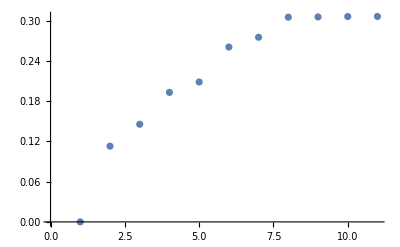

```mathematica
ListPlot[Table[Mean[differences038[[i]]],{i,1,11}]]
```

## Logging training on full MNIST set

### Net construction and logging

```mathematica
(* Defining a log to record weights, gradients, batch loss, and validation loss at training checkpoints. *)
logFileAll = CreateFile[];
appendToLogAll := PutAppend[ <|"Weights" -> #Weights,
				"Gradients" -> #Gradients, "BatchLoss" -> #BatchLoss, "ValidLoss" -> #ValidationLoss|>, logFileAll ]&
```

```mathematica
(* Training lenet on full MNIST set. Checkpointing occurs every 3 epochs. 
	NB: This took about 6 hours. *)
leNetTrainAll = NetTrain[
		lenet, 
		trainingData, 
		ValidationSet -> Scaled[0.1], 
		MaxTrainingRounds -> 100,
		BatchSize -> 100,
		TrainingProgressFunction -> {appendToLogAll, "Interval" -> Quantity[3, "Rounds"]}
	];
```

NetTrain::invnet: First argument to NetTrain should be a fully specified net.

### Training full MNIST accuracy

```mathematica
(* Accuracy on full test set. *)
accuracyAll = ClassifierMeasurements[ leNetTrainAll, testData, "Accuracy" ]
```

ClassifierMeasurements::wrgfunc: The first argument should be a ClassifierFunction instead of $Failed.

ClassifierMeasurements[$Failed,{-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,9920,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9},Accuracy]
 |  |  |  |

### Reading log full MNIST

```mathematica
(* Reading the checkpointing log. *)
logAll = ReadList[logFileAll];
```

```mathematica
(* Saving the net and log to disk. *)
Put[logAll, "2017_07_02_LogAll.mx"]
Export["2017_07_02_leNetTrainAll.wlnet",leNetTrainAll];
```

Export::invnet2: The second argument in Export[/Users/hikarisorensen/2017_07_02_leNetTrainAll.wlnet,$Failed] is not a valid net.

```mathematica
(* Get all weights at all training progress checkpoints (every 3 epochs). *) 
logAllW = Table[logAll[[i]]["Weights"],{i,Length[logAll]}];

(* Get all gradients at all training progress checkpoints (every 3 epochs). *) 
logAllG = Table[logAll[[i]]["Gradients"],{i,Length[logAll]}];
```

#### First conv. layer (1)

```mathematica
(* Among weights and gradients at each checkpoint, get the ones corresponding to the first (conv.) layer. *)
logAllW1W = Table[ logAllW[[i]][ {1, "Weights"} ], {i, Length[logAllW]}];
logAllG1W = Table[ logAllG[[i]][ {1, "Weights"} ], {i, Length[logAllG]}];
```

#### Second conv. layer (4)

```mathematica
(* Among weights and gradients at each checkpoint, get the ones corresponding to the 4th (conv.) layer. *)
logAllW4W = Table[ logAllW[[i]][ {4, "Weights"} ], {i, Length[logAllW]}];
logAllG4W = Table[ logAllG[[i]][ {4, "Weights"} ], {i, Length[logAllG]}];
```

#### First linear layer (8)

```mathematica
(* Among weights and gradients at each checkpoint, get the ones corresponding to the 8th (linear) layer. *)
logAllW8W = Table[ logAllW[[i]][ {8, "Weights"} ], {i, Length[logAllW]}];
logAllG8W = Table[ logAllG[[i]][ {8, "Weights"} ], {i, Length[logAllG]}];
```

#### Second linear layer (10)

```mathematica
(* Among weights and gradients at each checkpoint, get the ones corresponding to the 10th (linear) layer. *)
logAllW10W = Table[ logAllW[[i]][ {10, "Weights"} ], {i, Length[logAllW]}];
logAllG10W = Table[ logAllG[[i]][ {10, "Weights"} ], {i, Length[logAllG]}];
```

### Log full MNIST weight images

#### First conv. layer (1)

```mathematica
(* Turn the weights in the first layer into images. *)
logAllW1WImages = 
	Table[ 
		Map[
			Colorize[
				Image[
					Rescale[#, MinMax[logAllW1W], {0, 1}],
					Interleaving -> False, 
					ImageSize -> 20
				],
			(*ColorFunction -> ColorData["GrayTones"],*)
			ColorFunctionScaling -> False
		]&,
		logAllW1W[[i]]],
		{i, Length[logAllW1W]}
	];
```

Images of learned filters from first and last epoch of training on full MNIST set. Unlike for the 0, 3, 8 subset, we can see even with the human eye that the filters and changing.

```mathematica
Column[logAllW1WImages[[{1,33}]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Layer 1 filter difference plot

Here we log the differences in the images of the filters from epoch to epoch. There is indeed learning, and it follows a similar logarithmic curve to the 0, 3, 8 subset. The overall change in filters is greater than with the subset, however.

```mathematica
differencesAll = Table[
	Table[
		ImageDistance[logAllW1WImages[[1,i]],logAllW1WImages[[j,i]]],
	{i,Length[logAllW1WImages[[1]]]}]
	,{j,1,33}];
```

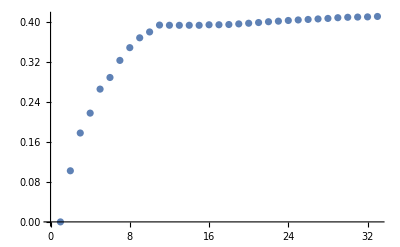

```mathematica
ListPlot[Table[Mean[differencesAll[[i]]],{i,1,33}]]
```

#### Second conv. layer (4)

```mathematica
dimAllW4W = Dimensions@logAllW4W
```

{33,50,20,5,5}

```mathematica
Clear[logAllW4WImages]
```

```mathematica
(* Turn the weights in the first layer into images. *)
logAllW4WImages[i_,j_,k_,size_] := 
	Return[
		Map[
			Colorize[
				Image[
					Rescale[#, MinMax[logAllW4W], {0, 1}],
					Interleaving -> False, 
					ImageSize -> size
				],
			(*ColorFunction -> ColorData["GrayTones"],*)
			ColorFunctionScaling -> False
		]&,
		{logAllW4W[[i, j, k]]}
	]
];
```

```mathematica
logAllW4WImages[1,2,3,10]
```

{-Graphics-}

```mathematica
(* Turn the weights in the 4th layer into images. *)
logAllW4WImages[i_, j_, k_, imagesize_] := 
	Return[
		Map[
			Colorize[
				Image[
					Rescale[#, MinMax[logAllW4W], {0, 1}],
					Interleaving -> False, 
					ImageSize -> imagesize
				],
			(*ColorFunction -> ColorData["GrayTones"],*)
			ColorFunctionScaling -> False
			]&,
		{logAllW4W[[i, j, k]]}
		][[1]]
	];
```

```mathematica
Dimensions@logAllW4W
```

{33,50,20,5,5}

```mathematica
Row[Flatten[Table[logAllW4WImages[i,j,k,size],{i,{1}},{j,{1}},{k,20},{size,{20}}]],Spacer[0.2]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

Images of learned filters from first and last epoch of training on full MNIST set. Unlike for the 0, 3, 8 subset, we can see even with the human eye that the filters and changing.

```mathematica
Column[logAllW4WImages[[{1,33}]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Flattened conv. images (7)

```mathematica
dimAllW4W = Dimensions@logAllW4W
```

{33,50,20,5,5}

```mathematica
flattenDim45 = Flatten[Flatten[logAllW4W, {4, 5}],{{2},{3},{4}}];
```

```mathematica
Dimensions@flattenDim45
```

{33,50,20,25}

```mathematica
flattenDim45Images[i_,j_,k_] := 
	Return[
		Map[
			Colorize[
				Image[
					Rescale[#, MinMax[logAllW4W], {0, 1}],
					Interleaving -> False, 
					Magnification -> 10
				],
			ColorFunctionScaling -> False
		]&,
		{{flattenDim45[[i, j, k]]}}
		]
	];
```

```mathematica
flattenDim45Images[1,1,1]
```

{-Graphics-}

#### First linear layer (8)

```mathematica
dimAllW8W = Dimensions@logAllW8W
```

{33,500,800}

```mathematica
(* Turn the weights in the 4th layer into images. *)
logAllW8WImages[i_, j_, mag_] := 
	Return[
		Map[
			Colorize[
				Image[
					Rescale[#, MinMax[logAllW8W], {0, 1}],
					Interleaving -> False, 
					Magnification -> mag
				],
			ColorFunctionScaling -> False
		]&,
		{Transpose[{logAllW8W[[i, j]]}]}
		][[1]]
	];
```

```mathematica
Row[Table[logAllW8WImages[1,i,5],{i,500}]]
```

{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}{-Graphics-}

```mathematica
Column@logAllW4WImages1[[1;;5]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* Turn the weights in the 4th layer into images. *)
logAllW4WImages = 
	Table[ 
		Map[
			Colorize[
				Image[
					Rescale[#, MinMax[logAllW4W], {0, 1}],
					Interleaving -> False, 
					ImageSize -> 20
				],
			(*ColorFunction -> ColorData["GrayTones"],*)
			ColorFunctionScaling -> False
		]&,
		logAllW4W[[i]][[All, j]]],
		{i, dimAllW4W[[1]]},
		{j, dimAllW4W[[3]]}
	];.
```

$Aborted

```mathematica
logAllW4WImages[[1]]
```

Images of learned filters from first and last epoch of training on full MNIST set. Unlike for the 0, 3, 8 subset, we can see even with the human eye that the filters and changing.

```mathematica
Column[logAllW4WImages[[{1,33}]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Log full MNIST convolved images

```mathematica
lenetLayers = {
	ConvolutionLayer[20, 5],
	Ramp,
	PoolingLayer[2, 2],
	ConvolutionLayer[50, 5],
	Ramp, 
	PoolingLayer[2, 2],
	FlattenLayer[],
	500,
	Ramp,
	10
	} (*,SoftmaxLayer[]}*);
```

```mathematica
netTable = Table[
			NetInitialize[
				NetChain[
					lenetLayers[[1 ;; i]],
					"Input" -> NetEncoder[{"Image", 28}],
					"Output" -> Automatic
				]
			],
			{i, Length[lenetLayers]}
		];
```

```mathematica
trainConvSample = RandomChoice[trainingData, 10];
```

```mathematica
Values[trainConvSample]
```

{7,0,2,3,3,5,2,5,2,0}

```mathematica
(* Displays progression through first 4 layers of first 10 training images (all 0's). 
	Convolved images shown, using 20 filters. *)

convolvedSample =
Table[
	Table[ Row[
		Table[
			Image[out, ImageSize -> 30],
			{out, netTable[[i]][dataPoint]}
		], Spacer[0.2]],
		{dataPoint, trainConvSample[[All, 1]]}
	],
	{i, 6}
];
```

#### Convolution 1

```mathematica
conv1 =Column[convolvedSample[[1]]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

#### Ramp 1 - negative weights go to 0

```mathematica
conv2 =Column[convolvedSample[[2]]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

#### Pooling 1

```mathematica
conv3 =Column[convolvedSample[[3]]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

#### Convolution 2 - each filter in first convolution gets convolved into 50 filters

```mathematica
conv4 = Column[convolvedSample[[4]]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

#### Pooling 2 - reduce to 4x4 image

```mathematica
conv6 = Column[convolvedSample[[6]]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

#### Flatten layer - flattens all 50 4x4 images of each training example into an 800-length feature vector

```mathematica
(* Displays progression through first 4 layers of first 10 training images (all 0's). 
	Convolved images shown, using 20 filters. *)

convolvedValues =
Table[
		Table[
			out, 
			{out, netTable[[6]][dataPoint]}
		],
		{dataPoint, trainConvSample[[All, 1]]}
];
```

```mathematica
Dimensions@convolvedValues[[1]]
```

{50,4,4}

```mathematica
featureVec[trainingPoint_] := 
	Return[
		Map[
			Colorize[
				Image[
					Rescale[#, MinMax[logAllW4W], {0, 1}],
					Interleaving -> False, 
					Magnification -> 5
				],
			ColorFunctionScaling -> False
		]&,
		{{Flatten[
			Table[
				out, 
				{out, netTable[[6]][trainingPoint[[1]]]}
			]
		]}}
		]
	];
```

```mathematica
randomSampleTrain = RandomSample[trainingData,10]
```

{-Graphics-→9,-Graphics-→0,-Graphics-→7,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→6,-Graphics-→1,-Graphics-→9,-Graphics-→2}

```mathematica
Column[Table[featureVec[data],{data,randomSampleTrain}]]
```

{-Graphics-}
{-Graphics-}
{-Graphics-}
{-Graphics-}
{-Graphics-}
{-Graphics-}
{-Graphics-}
{-Graphics-}
{-Graphics-}
{-Graphics-}

```mathematica
Column[Table[featureVec[data],{data,set0[[1;;5]]}]]
```

{-Graphics-}
{-Graphics-}
{-Graphics-}
{-Graphics-}
{-Graphics-}